# Phase-Leistung

## Funktionen

### Includes

```mathematica
<<"Labor.m"
```

## Geräteliste

Oszi: HM400 
true rms: Fluke 175 (A-Pr 10,11
normal: M-3850 voltcraft
Wattemeter: Feedback EW604

104, 47.2

## 1.) Spitzen und Effektivwerte für verschiedene Kurvenformen

```mathematica
f1= 50.0;
df1=0.1;
U1 = 10;
du1=1;
sin={{"Oszi", "true rms", "normal"}, {U1/(√2), 6.84, 6.78}}//N
drei={{"Oszi", "true rms", "normal"}, {U1/(√3), 5.70, 5.46}}//N
recht={{"Oszi", "true rms", "normal"}, {U1, 9.94, 10.96}}
```

(Oszi | true rms | normal
7.07107 | 6.84 | 6.78)

(Oszi | true rms | normal
5.7735 | 5.7 | 5.46)

(Oszi | true rms | normal
10 | 9.94 | 10.96)

```mathematica
1/√2//N
```

0.707107

```mathematica
U1 2/π//N
```

6.3662

## 2.) Phasenlage am Kondensator

Serienschaltung aus R und C. Stelltrafo als Spannungsquelle (U_eff=10V,50Hz).
Spannung an C messen und Strom durch U an R, am Oszi. Damit Phasenverschiebung bestimmen.

```mathematica
f2= 50;
df2=0;
U2 = 10.14; (*Effektivwert*)
t2=2.4*2*10^-3;
dt2=4*10^-4;
Ur = 13/(√2);
dur=1/(√2);
Uc=2.8/(√2);
duc=0.4/(√2);
(*ϕ2=t2*f2*2*π*)
ϕ2=Basic`Fmult[t2,dt2,f2,df2] *360//N;
```

```mathematica
Elec`Fϕ[Uc,duc,Ur,dur]*180/π
Elec`Fϕ[Uc √2,duc √2,Ur √2,dur √2]*180/π
```

{12.1549,2.59198}

{12.1549,2.59198}

```mathematica
ArcTan[-Uc/Ur]*180/π
1/(□/Ur+1)*180/π
```

-12.1549

180/(π ((√2 □)/13+1))

```mathematica
(150 50)/(150+50)//N
```

37.5

```mathematica
ArcTan[(1/(2 *π *50*130 *10^-6))/104]*180/π//N
```

13.2482

```mathematica
37.5+1/π*100
```

69.331

```mathematica
1/(2*π*50*100*10^-6)//N
```

31.831

## 3.) Wirkleistung in einer RC-Schaltung

### 3.1) 2 Parallele Widerstände

Gleicher Aufbau wie in 2. aber Widerstand durch 2 parallele ersetzen. (Wieviel Ω?)

```mathematica
f31= f2;
df31=0;
U31 = 10.04; (*Effektivwert*)
du31=0;
```

Spannung an R und C mit "true rms" messen.
Strom messen (ws wieder mit "true rms") und Kapazität berechnen.
100μ soll

```mathematica
Ur31 = 7.69;
Uc31 =5.765;
duc31=0;

I31 = 236.9*10^-3;
di31=0;

Ca31=(Elec`Fc[I31,du31,Uc31,duc31,f31,df31])/(2*π)
```

{0.000130802,0}

Scheinleistung:

```mathematica
PS31=Basic`Fmult[U31,du31,I31,di31]
```

{2.37848,Basic`GError(2.37848,{10.04,0.2369},{0,0})}

Mit Leistungsmessgerät Wirkleistung messen.

```mathematica
pw31 = 0.94*0.2*10
dpw31=0.02*0.2*10
```

1.88

0.04

Phase bestimmen. (ich nehm an mit Oszi)

```mathematica
t31=-2.4*2*10^-3;
dt31=4*10^-4;
ϕ31=Basic`Fmult[t31,dt31,f31,df31]*2*π
```

{-1.50796,2 π Basic`GError(-0.24,{-0.0048,50},{1/2500,0})}

Z_Ges in Gaußscher Zahlenebene darstellen.

{42.3808,Basic`GError(42.3808,{10.04,0.2369},{0,0})}

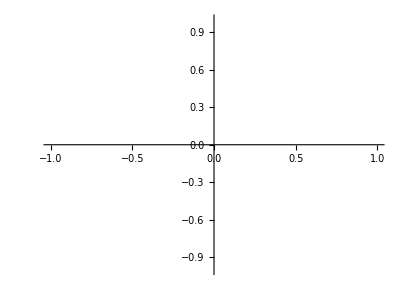

```mathematica
ZG31=Basic`Fdiv[U31,du31,I31,di31]
ListPolarPlot[{{0,0},{ϕ31,ZG31}},Joined-> True]
```